```mathematica
(* We want to investigate why quadrature of f[y] converges exponentially quick. The literature indicates periodic functions (and functions who have zero at boundaries (?)) have this property. *)
```

```mathematica
f[y_]:=(1 - Exp[-2 n(g+K/n-x2)(g-y)])PDF[NormalDistribution[0,1/(√n)],x2-y]*(1 - Exp[-2 n(g-y)(g - K/n-x0)])PDF[NormalDistribution[0,1/(√n)],x0-y]If[y<g,1,0]
```

```mathematica
f2[y_,x0_,x2_,n_,g_,K_]:=(1 - Exp[-2 n(g+K/n-x2)(g-y)])PDF[NormalDistribution[0,1/(√n)],x2-y]*(1 - Exp[-2 n(g-y)(g - K/n-x0)])PDF[NormalDistribution[0,1/(√n)],x0-y]If[y<g,1,0]
```

```mathematica
(* We see the derivative at the boundary is zero, regardless of x0 and x2. *)
```

```mathematica
Manipulate[Plot[f2[y,x0,x2,n,g,1] ,{y,-3,g},PlotRange->{{-3,3},{0,1}}],{x0,-1,g-1/n},{x2,-1,g + 1/n},{g,0.5,2},{n,3,10}]
```

```mathematica
(* Removing the indicator function*)
```

```mathematica
f2e[y_,x0_,x2_,n_,g_,K_]:=(1 - Exp[-2 n(g+K/n-x2)(g-y)])PDF[NormalDistribution[0,1/(√n)],x2-y]*(1 - Exp[-2 n(g-y)(g - K/n-x0)])PDF[NormalDistribution[0,1/(√n)],x0-y]
```

```mathematica
f2e[2,-1,-1,3,0.5,1]//N
```

0.477452

```mathematica
(* It appears that the function is symmetric around g*)
```

```mathematica
Manipulate[Plot[Abs[f2e[y,x0,x2,n,g,1] ],{y,-6,6},PlotRange->{{-9,9},{0,1}}],{x0,-1,3},{x2,-1,3},{g,0.5,2},{n,3,10}]
```

```mathematica
(*centering at g*)
```

```mathematica
Manipulate[Plot[Abs[f2e[y+g,x0,x2,n,g,1] ],{y,-6,6},PlotRange->{{-9,9},{0,1}}],{x0,-1,3},{x2,-1,3},{g,0.5,2},{n,3,10}]
```

```mathematica
f2ee[y_]:=(1 - Exp[-2 n(g+K/n-x2)(g-y)])PDF[NormalDistribution[0,1/(√n)],x2-y]*(1 - Exp[-2 n(g-y)(g - K/n-x0)])PDF[NormalDistribution[0,1/(√n)],x0-y]
```

```mathematica
Assuming[h >0 &&n>0 &&g>0 && Element[h, Reals]&& Element[K, Reals] && Element[g, Reals]&& Element[x0, Reals]&& Element[x2, Reals] && Element[n, Reals],FourierTransform[f2ee[t],t,s]]
```

(ⅇ^(-(4 g^2 n^2+4 ⅈ K s+s^2+2 ⅈ n s x0+n^2 x0^2+4 K n x2+2 ⅈ n s x2+2 n^2 x0 x2+n^2 x2^2)/(4 n)) (ⅇ^(g^2 n+2 ⅈ g s+(ⅈ K s)/n+K x2+n x0 x2)+ⅇ^(g^2 n+(ⅈ K s)/n+ⅈ s x0+K x2+ⅈ s x2+n x0 x2)-ⅇ^(K^2/n+ⅈ s x0+K ((2 ⅈ s)/n+x0)+g (ⅈ s+n (x0+x2)))-ⅇ^(K^2/n+K x0+ⅈ s x2+g (ⅈ s+n (x0+x2)))) √n)/(2 √2 π)

```mathematica
se[s_]:=(ⅇ^(-(4 g^2 n^2+4 ⅈ K s+s^2+2 ⅈ n s x0+n^2 x0^2+4 K n x2+2 ⅈ n s x2+2 n^2 x0 x2+n^2 x2^2)/(4 n)) (ⅇ^(g^2 n+2 ⅈ g s+(ⅈ K s)/n+K x2+n x0 x2)+ⅇ^(g^2 n+(ⅈ K s)/n+ⅈ s x0+K x2+ⅈ s x2+n x0 x2)-ⅇ^(K^2/n+ⅈ s x0+K ((2 ⅈ s)/n+x0)+g (ⅈ s+n (x0+x2)))-ⅇ^(K^2/n+K x0+ⅈ s x2+g (ⅈ s+n (x0+x2)))) √n)/(2 √2 π)
```

```mathematica
f2ee[0]/. g-> 1/. h-> 1/n /. x2-> 0.4/.x0-> 0.4/. K-> 1/.n -> 3//N
```

0.234926

```mathematica
se[0]/. g-> 1/. h-> 1/n /. x2-> 0.4/.x0-> 0.4/. K-> 1/.n -> 3//N
```

0.205082

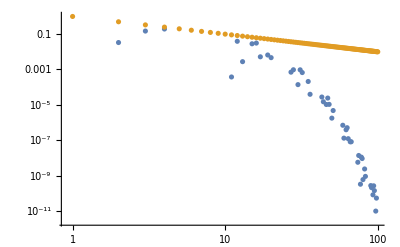

```mathematica
ListLogLogPlot[{Re[Table[∑_(k=-20)^20 se[k/h]-se[0]/. g-> 1/. h-> 1/n /. x2-> 0.4/.x0-> 0.4/. K-> 1//N,{n,1,100}]],Table[1/n,{n,1,100}]}]
```

```mathematica
f2eee[y_]:=f2ee[y+g]
```

```mathematica
Assuming[n>0 &&g>0 && Element[K, Reals] && Element[g, Reals]&& Element[x0, Reals]&& Element[x2, Reals] && Element[n, Reals],FourierTransform[f2eee[t],t,s,FourierParameters->{0,-2Pi}]]
```

(ⅇ^(-1/2 n (2 g^2+x0^2+x2^2-2 g (x0+x2))) (-ⅇ^((2 K-2 ⅈ π s+n x0-n x2)^2/(4 n))-ⅇ^((2 K+2 ⅈ π s+n x0-n x2)^2/(4 n))+ⅇ^((2 g n+2 ⅈ π s-n (x0+x2))^2/(4 n))+ⅇ^((-2 g n+2 ⅈ π s+n (x0+x2))^2/(4 n))) √n)/(2 √π)

```mathematica
sefinal[s_,n_]:=(ⅇ^(-1/2 n (2 g^2+x0^2+x2^2-2 g (x0+x2))) (-ⅇ^((2 K-2 ⅈ π s+n x0-n x2)^2/(4 n))-ⅇ^((2 K+2 ⅈ π s+n x0-n x2)^2/(4 n))+ⅇ^((2 g n+2 ⅈ π s-n (x0+x2))^2/(4 n))+ⅇ^((-2 g n+2 ⅈ π s+n (x0+x2))^2/(4 n))) √n)/(2 √π)
```

```mathematica
Table[∑_(k=-20)^20 sefinal[k/h,1]-sefinal[0]/. g-> 1/. h-> 1/n /. x2-> 0.4/.x0-> 0.4/. K-> 1//N,{n,1,10}]
```

{-0.304164+0. ⅈ,-0.568645+0. ⅈ,-0.710867+0. ⅈ,-0.818996+0. ⅈ,-0.907464+0. ⅈ,-0.982001+0. ⅈ,-1.04602+0. ⅈ,-1.10191+0. ⅈ,-1.15147+0. ⅈ,-1.19605+0. ⅈ}

```mathematica
Abs[Re[Table[∑_(k=-20)^20 sefinal[k/h,1]-sefinal[0]/. g-> 1/. h-> 1/n /. x2-> 0/.x0-> 0/. K-> 1//N,{n,1,20}]]]
```

{0.,0.247285,0.36276,0.439571,0.49915,0.549714,0.594877,0.636378,0.675144,0.711727,0.746489,0.779692,0.811532,0.842168,0.871727,0.900316,0.928025,0.95493,0.981097,1.00658}

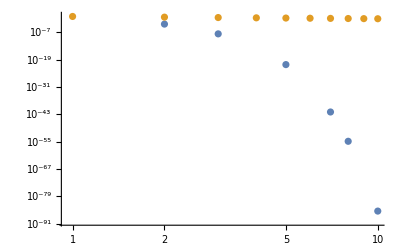

```mathematica
ListLogLogPlot[{Re[Table[∑_(k=-20)^20 sefinal[k/h,5]-sefinal[0,5]/. g-> 1/. h-> 1/M /. x2-> 0.4/.x0-> 0.4/. K-> 1//N,{M,1,10}]],Table[1/M,{M,1,10}]}]
```

```mathematica
NIntegrate[f2ee[y]/. g-> 1/. n -> 5 /. x2-> 0/.x0-> 0/. K-> 1,{y,-∞,1},WorkingPrecision->100]
```

0.6255919448981945432876402334174021228729671234482227025303227425905302710516752771948130027205359712

```mathematica
summand[y_,g_,n_,K_,x2_,x0_]:=(1 - Exp[-2 n(g+K/n-x2)(g-y)])PDF[NormalDistribution[0,1/(√n)],x2-y]*(1 - Exp[-2 n(g-y)(g - K/n-x0)])PDF[NormalDistribution[0,1/(√n)],x0-y]
```

```mathematica
s[h_,g_,n_]:=h∑_(k =-8/h)^(1/h) summand[k h,g,n,1,0,0]
```

```mathematica
N[s[1/300,1,5],100]
```

0.6255919448981945432876402334174021228729671234482227025303227425905302710516752771948130027205359712

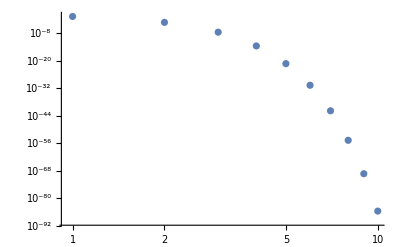

```mathematica
ListLogLogPlot[Table[Abs[NIntegrate[f2ee[y]/. g-> 1/. n -> 5 /. x2-> 0/.x0-> 0/. K-> 1,{y,-∞,1},WorkingPrecision->100] - N[s[1/M,1,5],100]],{M,1,10}]]
```

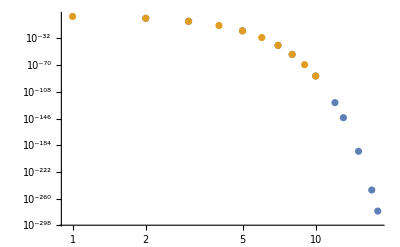

```mathematica
ListLogLogPlot[{Re[Table[∑_(k=-20)^20 sefinal[k/h,5]-sefinal[0,5]/. g-> 1/. h-> 1/M /. x2-> 0.4/.x0-> 0.4/. K-> 1//N,{M,1,50}]],Table[Abs[NIntegrate[f2ee[y]/. g-> 1/. n -> 5 /. x2-> 0/.x0-> 0/. K-> 1,{y,-∞,1},WorkingPrecision->100] -N[ s[1/M,1,5],100]],{M,1,50}]}]
```

```mathematica
(* If we zoom to y = g, we see there is a smooth transition to 0*)
```

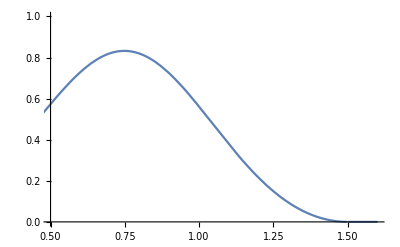

```mathematica
Plot[f2[y,0.6,0.9,6,1.5,1] ,{y,-3,1.6},PlotRange->{{0.5,1.6},{0,1}}]
```

```mathematica
f3[y_,x2_,n_,g_,K_]:=(1 - Exp[-2 n(g-x2)(g-y)])PDF[NormalDistribution[0,1/(√n)],x2-y]If[y<g,1,0]
```

```mathematica
(* As y approaches the boundary, the derivatives of the function explode. This is made even more extreme as we send x2 towards g also.*)
```

```mathematica
Manipulate[Plot[f3[y,x2,n,g,1] ,{y,-3,g},PlotRange->{{-3,3},{0,1}}],{x2,-1,g},{g,0.5,2},{n,3,10}]
```

```mathematica
(* As we send y x2 to g, *)
```

```mathematica
Evaluate[D[f3[y,x2,n,g,K],y]]/.y-> g
```

-ⅇ^(-1/2 n (-g+x2)^2) n^(3/2) √(2/π) (g-x2) If[g<g,1,0]

```mathematica
Manipulate[Plot[(1 - Exp[-2 n(g-x2)(g-y)])PDF[NormalDistribution[0,1/(√n)],x2-y] ,{y,-6,6},PlotRange->{{-6,6},{-1,1}}],{x2,-1,g},{g,0.5,2},{n,3,10}]
```

```mathematica
f3ee[y_]:=(1 - Exp[-2 n(g-x2)(g-y)])PDF[NormalDistribution[0,1/(√n)],x2-y]
```

```mathematica
Assuming[n>0 &&g>0 && Element[h, Reals]&& Element[K, Reals] && Element[g, Reals]&& Element[x0, Reals]&& Element[x2, Reals] && Element[n, Reals],FourierTransform[f3ee[t],t,s]]
```

(ⅇ^(-(s (s+2 ⅈ n x2))/(2 n)) (-ⅇ^(2 ⅈ g s)+ⅇ^(2 ⅈ s x2)))/(√(2 π))

```mathematica
se3[s_,n_]:=(ⅇ^(-(s (s+2 ⅈ n x2))/(2 n)) (-ⅇ^(2 ⅈ g s)+ⅇ^(2 ⅈ s x2)))/(√(2 π))
```

```mathematica
se3[10,3]/. x2-> 0.9999/. K-> 1/. g-> 1//N
```

-2.50792×10^-11+3.8681×10^-11 ⅈ

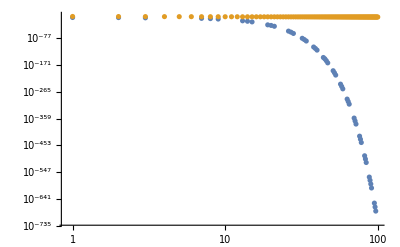

```mathematica
ListLogLogPlot[{Re[Table[∑_(k=-20)^20 se3[k/h,3]-se3[0,3]/. g-> 1/. h-> 1/n /. x2-> 0.9999/. K-> 1//N,{n,1,100}]],Table[1/n,{n,1,100}]}]
```

```mathematica
(*centered at g*)
```

```mathematica
f3eee[y_] := (ⅇ^(-1/2 n (-g+x2-y)^2) (1-ⅇ^(2 n (g-x2) y)) √n)/(√(2 π))
```

```mathematica
Assuming[n>0 &&g>0 && Element[h, Reals]&& Element[K, Reals] && Element[g, Reals]&& Element[x0, Reals]&& Element[x2, Reals] && Element[n, Reals],FourierTransform[f3eee[t],t,s]]
```

-ⅈ ⅇ^(-s^2/(2 n)) √(2/π) Sin[s (g-x2)]

```mathematica
se3eee[s_,n_]:=Abs[-ⅈ ⅇ^(-s^2/(2 n)) √(2/π) Sin[s (g-x2)] ⅇ^(-2π ⅈ g s)]
```

```mathematica
Abs[se3eee[1,3]/.g-> 1/.x2-> 0.5]
```

0.323801

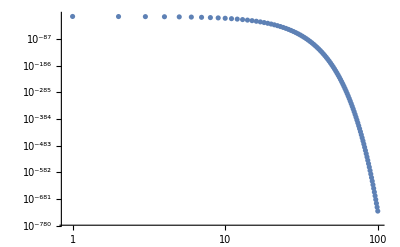

```mathematica
ListLogLogPlot[Re[Table[∑_(k=-20)^20 se3eee[k/h,3]-se3eee[0,3]/. g-> 1/. h-> 1/n /. x2-> 0.9999/. K-> 1//N,{n,1,100}]]]
```

```mathematica
(*Plotting  df/dx|_g for x2 ϵ[-3,g]. We see the derivative is non zero at the boundary if x2 is not equal to g or at negative infinity *)
```

```mathematica
Manipulate[Plot[Abs[-ⅇ^(-1/2 n (-g+x2)^2) n^(3/2) √(2/π) (g-x2) ] ,{x2,-3,g},PlotRange->{{-3,3},{0,2}}],{g,0.5,2},{n,3,10}]
```

```mathematica
Assuming[h >0 &&n>0 &&g>0 && Element[h, Reals]&& Element[K, Reals] && Element[g, Reals]&& Element[x0, Reals]&& Element[x2, Reals] && Element[n, Reals],∫_(-∞)^g (1 - Exp[-2 n(g+K/n-x2)(g-y)])PDF[NormalDistribution[0,1/(√n)],x2-y]*(1 - Exp[-2 n(g-y)(g - K/n-x0)])PDF[NormalDistribution[0,1/(√n)],x0-y] ⅇ^(-2π ⅈ s y)ⅆy]
```

1/(2 π)n (ⅇ^(-1/2 n (x0^2+x2^2)) (-ⅇ^(K^2/n-g^2 n-2 ⅈ g π s-(2 ⅈ K π s)/n-(π^2 s^2)/n+K x0+g n x0-ⅈ π s x0+(n x0^2)/4-K x2+g n x2+ⅈ π s x2-(n x0 x2)/2+(n x2^2)/4) ((√π)/(2 √n)-(√π (2 K+2 g n-2 ⅈ π s+n x0-n x2) Erf[(√((2 K+2 g n-2 ⅈ π s+n x0-n x2)^2))/(2 √n)])/(2 √n √((2 K+2 g n-2 ⅈ π s+n x0-n x2)^2)))-ⅇ^(K^2/n-g^2 n-2 ⅈ g π s+(2 ⅈ K π s)/n-(π^2 s^2)/n+K x0+g n x0+ⅈ π s x0+(n x0^2)/4-K x2+g n x2-ⅈ π s x2-(n x0 x2)/2+(n x2^2)/4) ((√π)/(2 √n)-(√π (-2 K+2 g n-2 ⅈ π s-n x0+n x2) Erf[(√((2 K-2 g n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)])/(2 √n √((2 K-2 g n+2 ⅈ π s+n x0-n x2)^2)))+ⅇ^(-(2 π s+ⅈ n x0+ⅈ n x2)^2/(4 n)) ((√π)/(2 √n)-(√π (-2 ⅈ π s+n (x0+x2)) Erf[(√((-2 ⅈ π s+n (x0+x2))^2))/(2 √n)])/(2 √n √((-2 ⅈ π s+n (x0+x2))^2)))+ⅇ^(-4 ⅈ g π s-(π^2 s^2)/n+ⅈ π s x0+(n x0^2)/4+ⅈ π s x2+(n x0 x2)/2+(n x2^2)/4) ((√π)/(2 √n)-(√π (4 g n-2 ⅈ π s-n (x0+x2)) Erf[(√((-4 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)])/(2 √n √((-4 g n+2 ⅈ π s+n (x0+x2))^2))))+ⅇ^(-1/2 n (x0^2+x2^2)) (-ⅇ^(K^2/n-g^2 n-2 ⅈ g π s-(2 ⅈ K π s)/n-(π^2 s^2)/n+K x0+g n x0-ⅈ π s x0+(n x0^2)/4-K x2+g n x2+ⅈ π s x2-(n x0 x2)/2+(n x2^2)/4) ((√π (-2 K+2 ⅈ π s+n (-x0+x2)) Erf[(√((2 K-2 ⅈ π s+n (x0-x2))^2))/(2 √n)])/(2 √n √((2 K-2 ⅈ π s+n (x0-x2))^2))+(√π (2 K+2 g n-2 ⅈ π s+n x0-n x2) Erf[(√((2 K+2 g n-2 ⅈ π s+n x0-n x2)^2))/(2 √n)])/(2 √n √((2 K+2 g n-2 ⅈ π s+n x0-n x2)^2)))-ⅇ^(K^2/n-g^2 n-2 ⅈ g π s+(2 ⅈ K π s)/n-(π^2 s^2)/n+K x0+g n x0+ⅈ π s x0+(n x0^2)/4-K x2+g n x2-ⅈ π s x2-(n x0 x2)/2+(n x2^2)/4) ((√π (2 K+2 ⅈ π s+n (x0-x2)) Erf[(√((2 K+2 ⅈ π s+n (x0-x2))^2))/(2 √n)])/(2 √n √((2 K+2 ⅈ π s+n (x0-x2))^2))-(√π (2 K-2 g n+2 ⅈ π s+n x0-n x2) Erf[(√((2 K-2 g n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)])/(2 √n √((2 K-2 g n+2 ⅈ π s+n x0-n x2)^2)))+ⅇ^((-2 ⅈ π s+n x0+n x2)^2/(4 n)) ((√π (2 g n+2 ⅈ π s-n (x0+x2)) Erf[(√((2 g n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)])/(2 √n √((2 g n+2 ⅈ π s-n (x0+x2))^2))+(√π (-2 ⅈ π s+n (x0+x2)) Erf[(√((-2 ⅈ π s+n (x0+x2))^2))/(2 √n)])/(2 √n √((-2 ⅈ π s+n (x0+x2))^2)))+ⅇ^(-4 ⅈ g π s-(π^2 s^2)/n+ⅈ π s x0+(n x0^2)/4+ⅈ π s x2+(n x0 x2)/2+(n x2^2)/4) (-(√π (-4 g n+2 ⅈ π s+n (x0+x2)) Erf[(√((-4 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)])/(2 √n √((-4 g n+2 ⅈ π s+n (x0+x2))^2))+(√π (-2 g n+2 ⅈ π s+n (x0+x2)) Erf[(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)])/(2 √n √((-2 g n+2 ⅈ π s+n (x0+x2))^2)))))

```mathematica
Assuming[h >0 &&n>0 &&g>0 && Element[h, Reals]&& Element[K, Reals] && Element[g, Reals]&& Element[x0, Reals]&& Element[x2, Reals] && Element[n, Reals],FourierCosTransform[f[t],t,s]]
```

1/(4 √2 π^(3/2))ⅇ^(-2 ⅈ g s-(ⅈ K s)/n-s^2/(4 n)-2 g n x0-(ⅈ s x0)/2-K x2-2 g n x2-(ⅈ s x2)/2-(n x0 x2)/2-1/2 n (8 g^2-4 g x0+x0^2-4 g x2+x2^2)) √n (-ⅇ^(4 g^2 n+(ⅈ K s)/n+(n x0^2)/4+K x2+n x0 x2+(n x2^2)/4+ⅈ s (x0+x2)) √π Erf[g √n-(ⅈ s)/(2 √n)-(√n x0)/2-(√n x2)/2]+ⅇ^(4 g^2 n+2 ⅈ g s+(ⅈ K s)/n+(n x0^2)/4+K x2+n x0 x2+(n x2^2)/4+ⅈ s (x0+x2)) √π Erf[g √n-(ⅈ s)/(2 √n)-(√n x0)/2-(√n x2)/2]+ⅇ^(4 g^2 n+(ⅈ K s)/n+(n x0^2)/4+K x2+n x0 x2+(n x2^2)/4+ⅈ s (x0+x2)) √π Erf[2 g √n-(ⅈ s)/(2 √n)-(√n x0)/2-(√n x2)/2]+ⅇ^(4 g^2 n+2 ⅈ g s+(ⅈ K s)/n+(n x0^2)/4+K x2+n x0 x2+(n x2^2)/4) √π Erf[g √n+(ⅈ s)/(2 √n)-(√n x0)/2-(√n x2)/2]-ⅇ^(4 g^2 n+4 ⅈ g s+(ⅈ K s)/n+(n x0^2)/4+K x2+n x0 x2+(n x2^2)/4) √π Erf[g √n+(ⅈ s)/(2 √n)-(√n x0)/2-(√n x2)/2]+ⅇ^(4 g^2 n+4 ⅈ g s+(ⅈ K s)/n+(n x0^2)/4+K x2+n x0 x2+(n x2^2)/4) √π Erf[2 g √n+(ⅈ s)/(2 √n)-(√n x0)/2-(√n x2)/2]+ⅇ^(K^2/n+3 g^2 n+ⅈ g s+K x0+g n x0+(n x0^2)/4+g n x2+ⅈ s x2+(n x2^2)/4) √π Erf[K/(√n)-(ⅈ s)/(2 √n)+(√n x0)/2-(√n x2)/2]-ⅇ^(K^2/n+3 g^2 n+ⅈ g s+K x0+g n x0+(n x0^2)/4+g n x2+(n x2^2)/4+ⅈ s (2 g+x2)) √π Erf[K/(√n)-(ⅈ s)/(2 √n)+(√n x0)/2-(√n x2)/2]+ⅇ^(K^2/n+3 g^2 n+ⅈ g s+K x0+g n x0+(n x0^2)/4+g n x2+(n x2^2)/4+ⅈ s (2 g+x2)) √π Erf[K/(√n)-g √n-(ⅈ s)/(2 √n)+(√n x0)/2-(√n x2)/2]-ⅇ^(K^2/n+3 g^2 n+ⅈ g s+K x0+g n x0+(n x0^2)/4+g n x2+ⅈ s x2+(n x2^2)/4) √π Erf[K/(√n)+g √n-(ⅈ s)/(2 √n)+(√n x0)/2-(√n x2)/2]-ⅇ^(K^2/n+3 g^2 n+ⅈ g s+K x0+g n x0+(n x0^2)/4+(ⅈ s (2 K+n x0))/n+g n x2+(n x2^2)/4) √π Erf[K/(√n)+(ⅈ s)/(2 √n)+(√n x0)/2-(√n x2)/2]+ⅇ^(K^2/n+3 g^2 n+ⅈ g s+K x0+g n x0+(n x0^2)/4+(ⅈ s (2 K+n (2 g+x0)))/n+g n x2+(n x2^2)/4) √π Erf[K/(√n)+(ⅈ s)/(2 √n)+(√n x0)/2-(√n x2)/2]+ⅇ^(K^2/n+3 g^2 n+ⅈ g s+K x0+g n x0+(n x0^2)/4+(ⅈ s (2 K+n x0))/n+g n x2+(n x2^2)/4) √π Erf[K/(√n)-g √n+(ⅈ s)/(2 √n)+(√n x0)/2-(√n x2)/2]-ⅇ^(K^2/n+3 g^2 n+ⅈ g s+K x0+g n x0+(n x0^2)/4+(ⅈ s (2 K+n (2 g+x0)))/n+g n x2+(n x2^2)/4) √π Erf[K/(√n)+g √n+(ⅈ s)/(2 √n)+(√n x0)/2-(√n x2)/2]+ⅈ ⅇ^(4 g^2 n+2 ⅈ g s+(ⅈ K s)/n+(n x0^2)/4+K x2+n x0 x2+(n x2^2)/4+ⅈ s (x0+x2)) √π Erfi[s/(2 √n)-1/2 ⅈ √n x0-1/2 ⅈ √n x2]-ⅈ ⅇ^(4 g^2 n+2 ⅈ g s+(ⅈ K s)/n+(n x0^2)/4+K x2+n x0 x2+(n x2^2)/4) √π Erfi[s/(2 √n)+1/2 ⅈ √n x0+1/2 ⅈ √n x2])

```mathematica
Assuming[h >0 &&n>0 &&g>0 && Element[h, Reals]&& Element[K, Reals] && Element[g, Reals]&& Element[x0, Reals]&& Element[x2, Reals] && Element[n, Reals],FourierTransform[f[t],t,s]]
```

(ⅇ^(-g^2 n-(ⅈ K s)/n-s^2/(4 n)-(ⅈ s x0)/2-(n x0^2)/4-K x2-(ⅈ s x2)/2-(n x0 x2)/2-(n x2^2)/4) √n (-ⅇ^(K^2/n+ⅈ g s+(2 ⅈ K s)/n+K x0+g n x0+ⅈ s x0+g n x2) √((2 g n-ⅈ s-n x0-n x2)^2) √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2)-ⅇ^(K^2/n+ⅈ g s+K x0+g n x0+g n x2+ⅈ s x2) √((2 g n-ⅈ s-n x0-n x2)^2) √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2)+ⅇ^(g^2 n+2 ⅈ g s+(ⅈ K s)/n+K x2+n x0 x2) √((2 g n-ⅈ s-n x0-n x2)^2) √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2)+ⅇ^(g^2 n+(ⅈ K s)/n+ⅈ s x0+K x2+ⅈ s x2+n x0 x2) √((2 g n-ⅈ s-n x0-n x2)^2) √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2)-2 ⅇ^(K^2/n+ⅈ g s+K x0+g n x0+g n x2+ⅈ s x2) K √((2 g n-ⅈ s-n x0-n x2)^2) √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2) Erf[(√((2 K-ⅈ s+n (x0-x2))^2))/(2 √n)]+ⅈ ⅇ^(K^2/n+ⅈ g s+K x0+g n x0+g n x2+ⅈ s x2) s √((2 g n-ⅈ s-n x0-n x2)^2) √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2) Erf[(√((2 K-ⅈ s+n (x0-x2))^2))/(2 √n)]-ⅇ^(K^2/n+ⅈ g s+K x0+g n x0+g n x2+ⅈ s x2) n x0 √((2 g n-ⅈ s-n x0-n x2)^2) √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2) Erf[(√((2 K-ⅈ s+n (x0-x2))^2))/(2 √n)]+ⅇ^(K^2/n+ⅈ g s+K x0+g n x0+g n x2+ⅈ s x2) n x2 √((2 g n-ⅈ s-n x0-n x2)^2) √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2) Erf[(√((2 K-ⅈ s+n (x0-x2))^2))/(2 √n)]+2 ⅇ^(K^2/n+ⅈ g s+(2 ⅈ K s)/n+K x0+g n x0+ⅈ s x0+g n x2) K √((2 g n-ⅈ s-n x0-n x2)^2) √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) Erf[(√((2 K+ⅈ s+n (x0-x2))^2))/(2 √n)]+ⅈ ⅇ^(K^2/n+ⅈ g s+(2 ⅈ K s)/n+K x0+g n x0+ⅈ s x0+g n x2) s √((2 g n-ⅈ s-n x0-n x2)^2) √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) Erf[(√((2 K+ⅈ s+n (x0-x2))^2))/(2 √n)]+ⅇ^(K^2/n+ⅈ g s+(2 ⅈ K s)/n+K x0+g n x0+ⅈ s x0+g n x2) n x0 √((2 g n-ⅈ s-n x0-n x2)^2) √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) Erf[(√((2 K+ⅈ s+n (x0-x2))^2))/(2 √n)]-ⅇ^(K^2/n+ⅈ g s+(2 ⅈ K s)/n+K x0+g n x0+ⅈ s x0+g n x2) n x2 √((2 g n-ⅈ s-n x0-n x2)^2) √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) Erf[(√((2 K+ⅈ s+n (x0-x2))^2))/(2 √n)]-2 ⅇ^(g^2 n+2 ⅈ g s+(ⅈ K s)/n+K x2+n x0 x2) g n √((2 g n-ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2) Erf[(√((2 g n+ⅈ s-n (x0+x2))^2))/(2 √n)]-ⅈ ⅇ^(g^2 n+2 ⅈ g s+(ⅈ K s)/n+K x2+n x0 x2) s √((2 g n-ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2) Erf[(√((2 g n+ⅈ s-n (x0+x2))^2))/(2 √n)]+ⅇ^(g^2 n+2 ⅈ g s+(ⅈ K s)/n+K x2+n x0 x2) n x0 √((2 g n-ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2) Erf[(√((2 g n+ⅈ s-n (x0+x2))^2))/(2 √n)]+ⅇ^(g^2 n+2 ⅈ g s+(ⅈ K s)/n+K x2+n x0 x2) n x2 √((2 g n-ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2) Erf[(√((2 g n+ⅈ s-n (x0+x2))^2))/(2 √n)]+2 ⅇ^(g^2 n+(ⅈ K s)/n+ⅈ s x0+K x2+ⅈ s x2+n x0 x2) g n √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2) Erf[(√((-2 g n+ⅈ s+n (x0+x2))^2))/(2 √n)]-ⅈ ⅇ^(g^2 n+(ⅈ K s)/n+ⅈ s x0+K x2+ⅈ s x2+n x0 x2) s √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2) Erf[(√((-2 g n+ⅈ s+n (x0+x2))^2))/(2 √n)]-ⅇ^(g^2 n+(ⅈ K s)/n+ⅈ s x0+K x2+ⅈ s x2+n x0 x2) n x0 √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2) Erf[(√((-2 g n+ⅈ s+n (x0+x2))^2))/(2 √n)]-ⅇ^(g^2 n+(ⅈ K s)/n+ⅈ s x0+K x2+ⅈ s x2+n x0 x2) n x2 √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2) Erf[(√((-2 g n+ⅈ s+n (x0+x2))^2))/(2 √n)]))/(4 √2 π √((2 g n-ⅈ s-n x0-n x2)^2) √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2))

```mathematica
F[s_]:=(ⅇ^(-g^2 n-(ⅈ K s)/n-s^2/(4 n)-(ⅈ s x0)/2-(n x0^2)/4-K x2-(ⅈ s x2)/2-(n x0 x2)/2-(n x2^2)/4) √n (-ⅇ^(K^2/n+ⅈ g s+(2 ⅈ K s)/n+K x0+g n x0+ⅈ s x0+g n x2) √((2 g n-ⅈ s-n x0-n x2)^2) √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2)-ⅇ^(K^2/n+ⅈ g s+K x0+g n x0+g n x2+ⅈ s x2) √((2 g n-ⅈ s-n x0-n x2)^2) √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2)+ⅇ^(g^2 n+2 ⅈ g s+(ⅈ K s)/n+K x2+n x0 x2) √((2 g n-ⅈ s-n x0-n x2)^2) √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2)+ⅇ^(g^2 n+(ⅈ K s)/n+ⅈ s x0+K x2+ⅈ s x2+n x0 x2) √((2 g n-ⅈ s-n x0-n x2)^2) √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2)-2 ⅇ^(K^2/n+ⅈ g s+K x0+g n x0+g n x2+ⅈ s x2) K √((2 g n-ⅈ s-n x0-n x2)^2) √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2) Erf[(√((2 K-ⅈ s+n (x0-x2))^2))/(2 √n)]+ⅈ ⅇ^(K^2/n+ⅈ g s+K x0+g n x0+g n x2+ⅈ s x2) s √((2 g n-ⅈ s-n x0-n x2)^2) √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2) Erf[(√((2 K-ⅈ s+n (x0-x2))^2))/(2 √n)]-ⅇ^(K^2/n+ⅈ g s+K x0+g n x0+g n x2+ⅈ s x2) n x0 √((2 g n-ⅈ s-n x0-n x2)^2) √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2) Erf[(√((2 K-ⅈ s+n (x0-x2))^2))/(2 √n)]+ⅇ^(K^2/n+ⅈ g s+K x0+g n x0+g n x2+ⅈ s x2) n x2 √((2 g n-ⅈ s-n x0-n x2)^2) √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2) Erf[(√((2 K-ⅈ s+n (x0-x2))^2))/(2 √n)]+2 ⅇ^(K^2/n+ⅈ g s+(2 ⅈ K s)/n+K x0+g n x0+ⅈ s x0+g n x2) K √((2 g n-ⅈ s-n x0-n x2)^2) √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) Erf[(√((2 K+ⅈ s+n (x0-x2))^2))/(2 √n)]+ⅈ ⅇ^(K^2/n+ⅈ g s+(2 ⅈ K s)/n+K x0+g n x0+ⅈ s x0+g n x2) s √((2 g n-ⅈ s-n x0-n x2)^2) √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) Erf[(√((2 K+ⅈ s+n (x0-x2))^2))/(2 √n)]+ⅇ^(K^2/n+ⅈ g s+(2 ⅈ K s)/n+K x0+g n x0+ⅈ s x0+g n x2) n x0 √((2 g n-ⅈ s-n x0-n x2)^2) √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) Erf[(√((2 K+ⅈ s+n (x0-x2))^2))/(2 √n)]-ⅇ^(K^2/n+ⅈ g s+(2 ⅈ K s)/n+K x0+g n x0+ⅈ s x0+g n x2) n x2 √((2 g n-ⅈ s-n x0-n x2)^2) √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) Erf[(√((2 K+ⅈ s+n (x0-x2))^2))/(2 √n)]-2 ⅇ^(g^2 n+2 ⅈ g s+(ⅈ K s)/n+K x2+n x0 x2) g n √((2 g n-ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2) Erf[(√((2 g n+ⅈ s-n (x0+x2))^2))/(2 √n)]-ⅈ ⅇ^(g^2 n+2 ⅈ g s+(ⅈ K s)/n+K x2+n x0 x2) s √((2 g n-ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2) Erf[(√((2 g n+ⅈ s-n (x0+x2))^2))/(2 √n)]+ⅇ^(g^2 n+2 ⅈ g s+(ⅈ K s)/n+K x2+n x0 x2) n x0 √((2 g n-ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2) Erf[(√((2 g n+ⅈ s-n (x0+x2))^2))/(2 √n)]+ⅇ^(g^2 n+2 ⅈ g s+(ⅈ K s)/n+K x2+n x0 x2) n x2 √((2 g n-ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2) Erf[(√((2 g n+ⅈ s-n (x0+x2))^2))/(2 √n)]+2 ⅇ^(g^2 n+(ⅈ K s)/n+ⅈ s x0+K x2+ⅈ s x2+n x0 x2) g n √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2) Erf[(√((-2 g n+ⅈ s+n (x0+x2))^2))/(2 √n)]-ⅈ ⅇ^(g^2 n+(ⅈ K s)/n+ⅈ s x0+K x2+ⅈ s x2+n x0 x2) s √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2) Erf[(√((-2 g n+ⅈ s+n (x0+x2))^2))/(2 √n)]-ⅇ^(g^2 n+(ⅈ K s)/n+ⅈ s x0+K x2+ⅈ s x2+n x0 x2) n x0 √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2) Erf[(√((-2 g n+ⅈ s+n (x0+x2))^2))/(2 √n)]-ⅇ^(g^2 n+(ⅈ K s)/n+ⅈ s x0+K x2+ⅈ s x2+n x0 x2) n x2 √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2) Erf[(√((-2 g n+ⅈ s+n (x0+x2))^2))/(2 √n)]))/(4 √2 π √((2 g n-ⅈ s-n x0-n x2)^2) √((2 g n+ⅈ s-n x0-n x2)^2) √((2 K-ⅈ s+n x0-n x2)^2) √((2 K+ⅈ s+n x0-n x2)^2))
```

```mathematica
F[1]/. g-> 1/. n-> 3/. h-> 3 /. x2-> 0.4/.x0-> 0.4/. K-> 1//N
```

0.151381+0.116017 ⅈ

```mathematica
∑_(k=-14)^14 F[k]/. g-> 1/. n-> 3/. h-> 3 /. x2-> 0.4/.x0-> 0.4/. K-> 1//N
```

0.588909-8.6228×10^-18 ⅈ

```mathematica
a = Table[∑_(k=-14)^14 F[k/h]/. g-> 1/. h-> 1/n /. x2-> 0.4/.x0-> 0.4/. K-> 1//N,{n,1,10}]
```

{-0.39962+2.36221×10^-17 ⅈ,0.0943245+1.10318×10^-17 ⅈ,0.196303+5.81827×10^-18 ⅈ,0.197348-3.24244×10^-18 ⅈ,0.175901+1.54976×10^-17 ⅈ,0.151928-2.22939×10^-18 ⅈ,0.152149-2.26835×10^-18 ⅈ,0.200543-1.7×10^-18 ⅈ,0.257698-5.38607×10^-18 ⅈ,0.310394+9.82474×10^-18 ⅈ}

```mathematica
Abs[Re[a]]
```

{0.39962,0.0943245,0.196303,0.197348,0.175901,0.151928,0.152149,0.200543,0.257698,0.310394}

```mathematica
G[s_]:=1/(2 π)n (ⅇ^(-1/2 n (x0^2+x2^2)) (-ⅇ^(K^2/n-g^2 n-2 ⅈ g π s-(2 ⅈ K π s)/n-(π^2 s^2)/n+K x0+g n x0-ⅈ π s x0+(n x0^2)/4-K x2+g n x2+ⅈ π s x2-(n x0 x2)/2+(n x2^2)/4) ((√π)/(2 √n)-(√π (2 K+2 g n-2 ⅈ π s+n x0-n x2) Erf[(√((2 K+2 g n-2 ⅈ π s+n x0-n x2)^2))/(2 √n)])/(2 √n √((2 K+2 g n-2 ⅈ π s+n x0-n x2)^2)))-ⅇ^(K^2/n-g^2 n-2 ⅈ g π s+(2 ⅈ K π s)/n-(π^2 s^2)/n+K x0+g n x0+ⅈ π s x0+(n x0^2)/4-K x2+g n x2-ⅈ π s x2-(n x0 x2)/2+(n x2^2)/4) ((√π)/(2 √n)-(√π (-2 K+2 g n-2 ⅈ π s-n x0+n x2) Erf[(√((2 K-2 g n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)])/(2 √n √((2 K-2 g n+2 ⅈ π s+n x0-n x2)^2)))+ⅇ^(-(2 π s+ⅈ n x0+ⅈ n x2)^2/(4 n)) ((√π)/(2 √n)-(√π (-2 ⅈ π s+n (x0+x2)) Erf[(√((-2 ⅈ π s+n (x0+x2))^2))/(2 √n)])/(2 √n √((-2 ⅈ π s+n (x0+x2))^2)))+ⅇ^(-4 ⅈ g π s-(π^2 s^2)/n+ⅈ π s x0+(n x0^2)/4+ⅈ π s x2+(n x0 x2)/2+(n x2^2)/4) ((√π)/(2 √n)-(√π (4 g n-2 ⅈ π s-n (x0+x2)) Erf[(√((-4 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)])/(2 √n √((-4 g n+2 ⅈ π s+n (x0+x2))^2))))+ⅇ^(-1/2 n (x0^2+x2^2)) (-ⅇ^(K^2/n-g^2 n-2 ⅈ g π s-(2 ⅈ K π s)/n-(π^2 s^2)/n+K x0+g n x0-ⅈ π s x0+(n x0^2)/4-K x2+g n x2+ⅈ π s x2-(n x0 x2)/2+(n x2^2)/4) ((√π (-2 K+2 ⅈ π s+n (-x0+x2)) Erf[(√((2 K-2 ⅈ π s+n (x0-x2))^2))/(2 √n)])/(2 √n √((2 K-2 ⅈ π s+n (x0-x2))^2))+(√π (2 K+2 g n-2 ⅈ π s+n x0-n x2) Erf[(√((2 K+2 g n-2 ⅈ π s+n x0-n x2)^2))/(2 √n)])/(2 √n √((2 K+2 g n-2 ⅈ π s+n x0-n x2)^2)))-ⅇ^(K^2/n-g^2 n-2 ⅈ g π s+(2 ⅈ K π s)/n-(π^2 s^2)/n+K x0+g n x0+ⅈ π s x0+(n x0^2)/4-K x2+g n x2-ⅈ π s x2-(n x0 x2)/2+(n x2^2)/4) ((√π (2 K+2 ⅈ π s+n (x0-x2)) Erf[(√((2 K+2 ⅈ π s+n (x0-x2))^2))/(2 √n)])/(2 √n √((2 K+2 ⅈ π s+n (x0-x2))^2))-(√π (2 K-2 g n+2 ⅈ π s+n x0-n x2) Erf[(√((2 K-2 g n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)])/(2 √n √((2 K-2 g n+2 ⅈ π s+n x0-n x2)^2)))+ⅇ^((-2 ⅈ π s+n x0+n x2)^2/(4 n)) ((√π (2 g n+2 ⅈ π s-n (x0+x2)) Erf[(√((2 g n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)])/(2 √n √((2 g n+2 ⅈ π s-n (x0+x2))^2))+(√π (-2 ⅈ π s+n (x0+x2)) Erf[(√((-2 ⅈ π s+n (x0+x2))^2))/(2 √n)])/(2 √n √((-2 ⅈ π s+n (x0+x2))^2)))+ⅇ^(-4 ⅈ g π s-(π^2 s^2)/n+ⅈ π s x0+(n x0^2)/4+ⅈ π s x2+(n x0 x2)/2+(n x2^2)/4) (-(√π (-4 g n+2 ⅈ π s+n (x0+x2)) Erf[(√((-4 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)])/(2 √n √((-4 g n+2 ⅈ π s+n (x0+x2))^2))+(√π (-2 g n+2 ⅈ π s+n (x0+x2)) Erf[(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)])/(2 √n √((-2 g n+2 ⅈ π s+n (x0+x2))^2)))))
```

```mathematica
Simplify[G[k]]
```

1/(4 √π)ⅇ^(-1/2 n (x0^2+x2^2)) √n ((ⅇ^(K^2/n-g^2 n+(-2 ⅈ k π+n (x0-x2))^2/(4 n)+K (-(2 ⅈ k π)/n+x0-x2)+g (-2 ⅈ k π+n (x0+x2))) (-√((2 K+2 g n-2 ⅈ k π+n x0-n x2)^2)+(2 K+2 g n-2 ⅈ k π+n x0-n x2) Erf[(√((2 K+2 g n-2 ⅈ k π+n x0-n x2)^2))/(2 √n)]))/(√((2 K+2 g n-2 ⅈ k π+n x0-n x2)^2))-ⅇ^(K^2/n-g^2 n+(-2 ⅈ k π+n (x0-x2))^2/(4 n)+K (-(2 ⅈ k π)/n+x0-x2)+g (-2 ⅈ k π+n (x0+x2))) (((-2 K+2 ⅈ k π+n (-x0+x2)) Erf[(√((2 K-2 ⅈ k π+n x0-n x2)^2))/(2 √n)])/(√((2 K-2 ⅈ k π+n (x0-x2))^2))+((2 K+2 g n-2 ⅈ k π+n x0-n x2) Erf[(√((2 K+2 g n-2 ⅈ k π+n x0-n x2)^2))/(2 √n)])/(√((2 K+2 g n-2 ⅈ k π+n x0-n x2)^2)))-(ⅇ^(K^2/n-g^2 n+(2 ⅈ k π+n (x0-x2))^2/(4 n)+K ((2 ⅈ k π)/n+x0-x2)+g (-2 ⅈ k π+n (x0+x2))) (√((2 K-2 g n+2 ⅈ k π+n x0-n x2)^2)+(2 K-2 g n+2 ⅈ k π+n x0-n x2) Erf[(√((2 K-2 g n+2 ⅈ k π+n x0-n x2)^2))/(2 √n)]))/(√((2 K-2 g n+2 ⅈ k π+n x0-n x2)^2))+ⅇ^(K^2/n-g^2 n+(2 ⅈ k π+n (x0-x2))^2/(4 n)+K ((2 ⅈ k π)/n+x0-x2)+g (-2 ⅈ k π+n (x0+x2))) (-((2 K+2 ⅈ k π+n (x0-x2)) Erf[(√((2 K+2 ⅈ k π+n x0-n x2)^2))/(2 √n)])/(√((2 K+2 ⅈ k π+n (x0-x2))^2))+((2 K-2 g n+2 ⅈ k π+n x0-n x2) Erf[(√((2 K-2 g n+2 ⅈ k π+n x0-n x2)^2))/(2 √n)])/(√((2 K-2 g n+2 ⅈ k π+n x0-n x2)^2)))+ⅇ^((-2 ⅈ k π+n (x0+x2))^2/(4 n)) (1-((-2 ⅈ k π+n (x0+x2)) Erf[(√((-2 ⅈ k π+n (x0+x2))^2))/(2 √n)])/(√((-2 ⅈ k π+n (x0+x2))^2)))+ⅇ^((-2 ⅈ k π+n (x0+x2))^2/(4 n)) (((2 g n+2 ⅈ k π-n (x0+x2)) Erf[(√((2 g n+2 ⅈ k π-n (x0+x2))^2))/(2 √n)])/(√((2 g n+2 ⅈ k π-n (x0+x2))^2))+((-2 ⅈ k π+n (x0+x2)) Erf[(√((-2 ⅈ k π+n (x0+x2))^2))/(2 √n)])/(√((-2 ⅈ k π+n (x0+x2))^2)))+(ⅇ^(-4 ⅈ g k π+(2 ⅈ k π+n (x0+x2))^2/(4 n)) (√((-4 g n+2 ⅈ k π+n (x0+x2))^2)+(-4 g n+2 ⅈ k π+n (x0+x2)) Erf[(√((-4 g n+2 ⅈ k π+n (x0+x2))^2))/(2 √n)]))/(√((-4 g n+2 ⅈ k π+n (x0+x2))^2))+ⅇ^(-4 ⅈ g k π+(2 ⅈ k π+n (x0+x2))^2/(4 n)) (((4 g n-2 ⅈ k π-n (x0+x2)) Erf[(√((-4 g n+2 ⅈ k π+n (x0+x2))^2))/(2 √n)])/(√((-4 g n+2 ⅈ k π+n (x0+x2))^2))-((2 g n-2 ⅈ k π-n (x0+x2)) Erf[(√((-2 g n+2 ⅈ k π+n (x0+x2))^2))/(2 √n)])/(√((-2 g n+2 ⅈ k π+n (x0+x2))^2))))

```mathematica
b = Table[∑_(k=-14)^14 G[k/h]/. g-> 1/. h-> 1/n /. x2-> 0.4/.x0-> 0.4/. K-> 1//N,{n,1,10}]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating √π/2.

General::stop: Further output of N :: meprec will be suppressed during this calculation.

Power::infy: Infinite expression 1/√0. encountered.

Infinity::indet: Indeterminate expression 0.\ √π\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/√0. encountered.

Infinity::indet: Indeterminate expression 0.\ √π\ ComplexInfinity encountered.

{Indeterminate,0.0787584+1.52466×10^-20 ⅈ,0.256855+1.0842×10^-19 ⅈ,0.392347-1.01644×10^-19 ⅈ,0.503256+0. ⅈ,0.596597-4.33681×10^-19 ⅈ,0.676865+4.33681×10^-19 ⅈ,0.746948+0. ⅈ,0.809076+8.02564×10^-20 ⅈ,0.864979+2.5411×10^-21 ⅈ}

```mathematica
integ[n_]:=NIntegrate[(1 - Exp[-2 n(g+K/n-x2)(g-y)])PDF[NormalDistribution[0,1/(√n)],x2-y]*(1 - Exp[-2 n(g-y)(g - K/n-x0)])PDF[NormalDistribution[0,1/(√n)],x0-y] /. g-> 3 /. K-> 0.3 /. x2 -> 0.5 /.x0->0.5,{y,-∞,3}]
```

```mathematica
s[n_,h_]:=h∑_(y=-3/h)^(1/h) ((1 - Exp[-2 n(g+K/n-x2)(g-y h)])PDF[NormalDistribution[0,1/(√n)],x2-y h]*(1 - Exp[-2 n(g-y h)(g - K/n-x0)])PDF[NormalDistribution[0,1/(√n)],x0-y h] )//N
```

```mathematica
Abs[integ[3] - s[3,1/3] /. g-> 3 /. K-> 0.3 /. x2 -> 0.5 /.x0->0.5]
```

0.0226922

```mathematica
N[integ[3],10]
```

0.488603

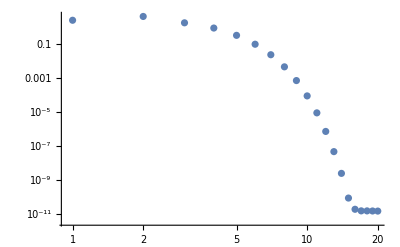

```mathematica
ListLogLogPlot[Table[Abs[integ[90] - s[90,1/n] /. g-> 3 /. K-> 0.3 /. x2 -> 0.5 /.x0->0.5] ,{n,1,20}]]
```

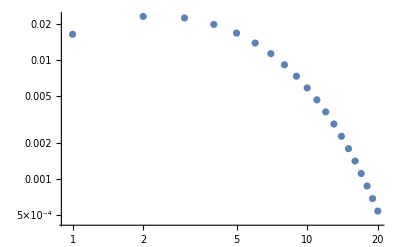

```mathematica
ListLogLogPlot[Table[Abs[integ[n] - s[n] /. g-> 3 /. K-> 0.3 /. x2 -> 0.5 /.x0->0.5] ,{n,1,20}]]
```

```mathematica
H[s_]:=1/(4 √2 π^(3/2))ⅇ^(-2 ⅈ g s-(ⅈ K s)/n-s^2/(4 n)-2 g n x0-(ⅈ s x0)/2-K x2-2 g n x2-(ⅈ s x2)/2-(n x0 x2)/2-1/2 n (8 g^2-4 g x0+x0^2-4 g x2+x2^2)) √n (-ⅇ^(4 g^2 n+(ⅈ K s)/n+(n x0^2)/4+K x2+n x0 x2+(n x2^2)/4+ⅈ s (x0+x2)) √π Erf[g √n-(ⅈ s)/(2 √n)-(√n x0)/2-(√n x2)/2]+ⅇ^(4 g^2 n+2 ⅈ g s+(ⅈ K s)/n+(n x0^2)/4+K x2+n x0 x2+(n x2^2)/4+ⅈ s (x0+x2)) √π Erf[g √n-(ⅈ s)/(2 √n)-(√n x0)/2-(√n x2)/2]+ⅇ^(4 g^2 n+(ⅈ K s)/n+(n x0^2)/4+K x2+n x0 x2+(n x2^2)/4+ⅈ s (x0+x2)) √π Erf[2 g √n-(ⅈ s)/(2 √n)-(√n x0)/2-(√n x2)/2]+ⅇ^(4 g^2 n+2 ⅈ g s+(ⅈ K s)/n+(n x0^2)/4+K x2+n x0 x2+(n x2^2)/4) √π Erf[g √n+(ⅈ s)/(2 √n)-(√n x0)/2-(√n x2)/2]-ⅇ^(4 g^2 n+4 ⅈ g s+(ⅈ K s)/n+(n x0^2)/4+K x2+n x0 x2+(n x2^2)/4) √π Erf[g √n+(ⅈ s)/(2 √n)-(√n x0)/2-(√n x2)/2]+ⅇ^(4 g^2 n+4 ⅈ g s+(ⅈ K s)/n+(n x0^2)/4+K x2+n x0 x2+(n x2^2)/4) √π Erf[2 g √n+(ⅈ s)/(2 √n)-(√n x0)/2-(√n x2)/2]+ⅇ^(K^2/n+3 g^2 n+ⅈ g s+K x0+g n x0+(n x0^2)/4+g n x2+ⅈ s x2+(n x2^2)/4) √π Erf[K/(√n)-(ⅈ s)/(2 √n)+(√n x0)/2-(√n x2)/2]-ⅇ^(K^2/n+3 g^2 n+ⅈ g s+K x0+g n x0+(n x0^2)/4+g n x2+(n x2^2)/4+ⅈ s (2 g+x2)) √π Erf[K/(√n)-(ⅈ s)/(2 √n)+(√n x0)/2-(√n x2)/2]+ⅇ^(K^2/n+3 g^2 n+ⅈ g s+K x0+g n x0+(n x0^2)/4+g n x2+(n x2^2)/4+ⅈ s (2 g+x2)) √π Erf[K/(√n)-g √n-(ⅈ s)/(2 √n)+(√n x0)/2-(√n x2)/2]-ⅇ^(K^2/n+3 g^2 n+ⅈ g s+K x0+g n x0+(n x0^2)/4+g n x2+ⅈ s x2+(n x2^2)/4) √π Erf[K/(√n)+g √n-(ⅈ s)/(2 √n)+(√n x0)/2-(√n x2)/2]-ⅇ^(K^2/n+3 g^2 n+ⅈ g s+K x0+g n x0+(n x0^2)/4+(ⅈ s (2 K+n x0))/n+g n x2+(n x2^2)/4) √π Erf[K/(√n)+(ⅈ s)/(2 √n)+(√n x0)/2-(√n x2)/2]+ⅇ^(K^2/n+3 g^2 n+ⅈ g s+K x0+g n x0+(n x0^2)/4+(ⅈ s (2 K+n (2 g+x0)))/n+g n x2+(n x2^2)/4) √π Erf[K/(√n)+(ⅈ s)/(2 √n)+(√n x0)/2-(√n x2)/2]+ⅇ^(K^2/n+3 g^2 n+ⅈ g s+K x0+g n x0+(n x0^2)/4+(ⅈ s (2 K+n x0))/n+g n x2+(n x2^2)/4) √π Erf[K/(√n)-g √n+(ⅈ s)/(2 √n)+(√n x0)/2-(√n x2)/2]-ⅇ^(K^2/n+3 g^2 n+ⅈ g s+K x0+g n x0+(n x0^2)/4+(ⅈ s (2 K+n (2 g+x0)))/n+g n x2+(n x2^2)/4) √π Erf[K/(√n)+g √n+(ⅈ s)/(2 √n)+(√n x0)/2-(√n x2)/2]+ⅈ ⅇ^(4 g^2 n+2 ⅈ g s+(ⅈ K s)/n+(n x0^2)/4+K x2+n x0 x2+(n x2^2)/4+ⅈ s (x0+x2)) √π Erfi[s/(2 √n)-1/2 ⅈ √n x0-1/2 ⅈ √n x2]-ⅈ ⅇ^(4 g^2 n+2 ⅈ g s+(ⅈ K s)/n+(n x0^2)/4+K x2+n x0 x2+(n x2^2)/4) √π Erfi[s/(2 √n)+1/2 ⅈ √n x0+1/2 ⅈ √n x2])
```

```mathematica
c = Table[∑_(k=-14)^14 H[k/h]/. g-> 1/. h-> 1/n /. x2-> 0.4/.x0-> 0.4/. K-> 1//N,{n,1,10}]
```

{-0.385645+1.41328×10^-17 ⅈ,0.0958432+2.25096×10^-17 ⅈ,0.202003+5.65469×10^-18 ⅈ,0.20388-5.41942×10^-18 ⅈ,0.18195-2.23584×10^-18 ⅈ,0.157262-3.75607×10^-18 ⅈ,0.1789-7.95467×10^-18 ⅈ,0.294101-4.81539×10^-18 ⅈ,0.424192-7.40718×10^-18 ⅈ,0.543053-1.25512×10^-18 ⅈ}

```mathematica
a = Table[∑_(k=-14)^14 F[k/h]/. g-> 1/. h-> 1/n /. x2-> 0.4/.x0-> 0.4/. K-> 1//N,{n,1,10}]
```

{-0.39962+2.36221×10^-17 ⅈ,0.0943245+1.10318×10^-17 ⅈ,0.196303+5.81827×10^-18 ⅈ,0.197348-3.24244×10^-18 ⅈ,0.175901+1.54976×10^-17 ⅈ,0.151928-2.22939×10^-18 ⅈ,0.152149-2.26835×10^-18 ⅈ,0.200543-1.7×10^-18 ⅈ,0.257698-5.38607×10^-18 ⅈ,0.310394+9.82474×10^-18 ⅈ}